# Graph of the map of Colombia

```mathematica
edges=Import["https://github.com/dfcheca/colombia-coloring/raw/main/dataset/colombia.dat","Table"];
```

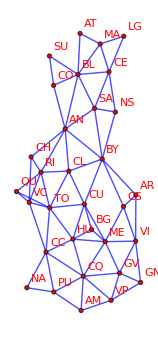

```mathematica
g=Graph[UndirectedEdge@@@edges];
coords=GraphEmbedding[g];
rotatedCoords={{0,1},{-1,0}}.#&/@coords;
reflectedCoords={{-1,0},{0,1}}.#&/@rotatedCoords;
G=Graph[UndirectedEdge@@@edges,VertexCoordinates->reflectedCoords,VertexLabels->"Name",VertexStyle->Directive[Red],EdgeStyle->Blue]
```

```mathematica
ChromaticPolynomial[G,t]t /.t->4
```

283115520

Chromatic Polynomial of the map (graph) of Colombia

```mathematica
ChromaticPolynomial[G,t]t (*It's necessary to multiply by t to also consider San Andrés y Providencia*)//Expand
```

-961919815680 t^2+11673935115264 t^3-68636197988352 t^4+260520144880896 t^5-717670769635584 t^6+1529179876264320 t^7-2622562341468416 t^8+3719159851081504 t^9-4446080022163760 t^10+4544515915061124 t^11-4014284821039240 t^12+3089197236230153 t^13-2083729861163011 t^14+1237494226626151 t^15-649111128011288 t^16+301323104920452 t^17-123904692011141 t^18+45128702300210 t^19-14543216293518 t^20+4137985048853 t^21-1036142031322 t^22+227281194275 t^23-43406309014 t^24+7159276765 t^25-1008989839 t^26+119803182 t^27-11757140 t^28+928416 t^29-56703 t^30+2514 t^31-72 t^32+t^33

```mathematica
Col[t_]:=-961919815680 t^2+11673935115264 t^3-68636197988352 t^4+260520144880896 t^5-717670769635584 t^6+1529179876264320 t^7-2622562341468416 t^8+3719159851081504 t^9-4446080022163760 t^10+4544515915061124 t^11-4014284821039240 t^12+3089197236230153 t^13-2083729861163011 t^14+1237494226626151 t^15-649111128011288 t^16+301323104920452 t^17-123904692011141 t^18+45128702300210 t^19-14543216293518 t^20+4137985048853 t^21-1036142031322 t^22+227281194275 t^23-43406309014 t^24+7159276765 t^25-1008989839 t^26+119803182 t^27-11757140 t^28+928416 t^29-56703 t^30+2514 t^31-72 t^32+t^33
```

```mathematica
Col[3](*It cannot be colored using just three colors*)
```

0

```mathematica
Col[4]
```

283115520